## Dunaev Viktor, 3 kurs, 6 group , Variant 23

## Task 1

## Create.

## Task 2

```mathematica
fname = NotebookDirectory[]<>"input.txt"
```

C:\Users\Виктор\Downloads\input.txt

```mathematica
stream = OpenRead[fname];
```

```mathematica
information = ReadList[stream,String]
```

{/*|I|*/ 6,/*|U|*/ 12,{1,5},{2,5},{3,1},{3,4},{3,5},{4,1},{4,2},{4,6},{5,4},{6,2},{6,3},{6,5},/*b_1*/ 7,/*b_2*/ 4,/*b_3*/ -1,/*b_4*/ -7,/*b_5*/ -2,/*b_6*/ -1}

```mathematica
numVertex = Read[StringToStream[StringSplit[information⟦1⟧]⟦2⟧],Number]
```

6

```mathematica
MyVertex = Table[i,{i,1,numVertex}]
```

{1,2,3,4,5,6}

```mathematica
numEdges = Read[StringToStream[StringSplit[information⟦2⟧]⟦2⟧],Number]
```

12

```mathematica
MyEdges = Table[
list = StringSplit[information⟦i⟧,{"{","}",","}];
Read[StringToStream[list⟦1⟧],Number]->Read[StringToStream[list⟦2⟧],Number],
{i,3,2+numEdges}
]
```

{1→5,2→5,3→1,3→4,3→5,4→1,4→2,4→6,5→4,6→2,6→3,6→5}

```mathematica
Close[stream]
```

C:\Users\Виктор\Downloads\input.txt

## Task 3

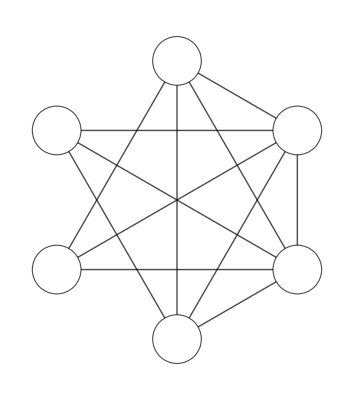

```mathematica
myGraph = Graph[MyVertex,MyEdges,VertexLabels->Placed["Name",Center], GraphLayout->"CircularEmbedding",VertexSize->0.35, VertexStyle->White,EdgeShapeFunction->GraphElementData["Arrow","ArrowSize"->0.035],EdgeStyle->Black,VertexLabelStyle->Large]
```

## Task 4

```mathematica
MyB = Table[
Read[StringToStream[StringSplit[information⟦i⟧]⟦2⟧],Number],
{i,3+numEdges,Length[information]}
]
```

{7,4,-1,-7,-2,-1}

```mathematica
MySystem=Total/@(Subscript[x,#]&/@Select[MyEdges,MatchQ[#->_]]&/@MyVertex)-Total/@(Subscript[x,#]&/@Select[MyEdges,MatchQ[_->#]]&/@MyVertex)
```

{x_(1→5)-x_(3→1)-x_(4→1),x_(2→5)-x_(4→2)-x_(6→2),x_(3→1)+x_(3→4)+x_(3→5)-x_(6→3),-x_(3→4)+x_(4→1)+x_(4→2)+x_(4→6)-x_(5→4),-x_(1→5)-x_(2→5)-x_(3→5)+x_(5→4)-x_(6→5),-x_(4→6)+x_(6→2)+x_(6→3)+x_(6→5)}

```mathematica
MySystem=(MySystem[[#]]==MyB[[#]])&/@MyVertex
```

{x_(1→5)-x_(3→1)-x_(4→1)==7,x_(2→5)-x_(4→2)-x_(6→2)==4,x_(3→1)+x_(3→4)+x_(3→5)-x_(6→3)==-1,-x_(3→4)+x_(4→1)+x_(4→2)+x_(4→6)-x_(5→4)==-7,-x_(1→5)-x_(2→5)-x_(3→5)+x_(5→4)-x_(6→5)==-2,-x_(4→6)+x_(6→2)+x_(6→3)+x_(6→5)==-1}

```mathematica
TableForm[MySystem]
```

x_(1→5)-x_(3→1)-x_(4→1)==7
x_(2→5)-x_(4→2)-x_(6→2)==4
x_(3→1)+x_(3→4)+x_(3→5)-x_(6→3)==-1
-x_(3→4)+x_(4→1)+x_(4→2)+x_(4→6)-x_(5→4)==-7
-x_(1→5)-x_(2→5)-x_(3→5)+x_(5→4)-x_(6→5)==-2
-x_(4→6)+x_(6→2)+x_(6→3)+x_(6→5)==-1

## Task 5

```mathematica
MySolve = Solve[MySystem]
```

{{x_(4→1)→-7+x_(1→5)-x_(3→1),x_(5→4)→x_(1→5)-x_(3→1)-x_(3→4)+x_(4→2)+x_(4→6),x_(6→2)→-4+x_(2→5)-x_(4→2),x_(6→3)→1+x_(3→1)+x_(3→4)+x_(3→5),x_(6→5)→2-x_(2→5)-x_(3→1)-x_(3→4)-x_(3→5)+x_(4→2)+x_(4→6)}}

```mathematica
Simplify[MySystem /. MySolve]
```

{{True,True,True,True,True,True}}